```mathematica
c=x(1-x)*y(1-y)
```

(1-x) x (1-y) y

```mathematica
u=-x
```

-x

```mathematica
v=y
```

y

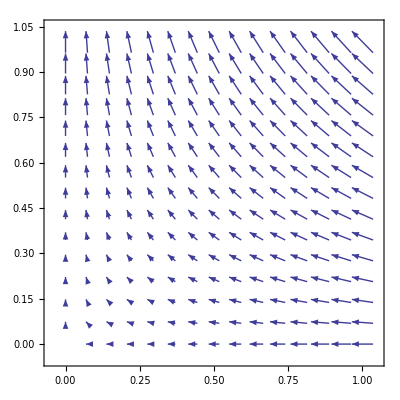

```mathematica
VectorPlot[{u,v},{x,0,1},{y,0,1}]
```

```mathematica
Clear[eps]
```

```mathematica
Simplify[-eps (D[c,{x,2}]+D[c,{y,2}])+{u,v}.{D[c,x],D[c,y]}]
```

x (x-y) y-2 eps (-x+x^2+(-1+y) y)